## Just testing the new Package.

```mathematica
Clear["*`"]
FindFile["GravWavesFunctions.m"]
```

/home/gabella/Documents/astro/exop/GravWavesFunctions.m

```mathematica
Get["/home/gabella/Documents/astro/exop/GravWavesFunctions.m"]
```

2955.43 meters per solar mass, Schwarzschild for sun.

1477.71 meters per solar mass, G=c=1 units.

```mathematica
Needs["GravWaves`GWConstants`"]
```

```mathematica
?"GravWaves`GWConstants`*"
```

```mathematica
cee
```

2.99792×10^8

```mathematica
Names["GravWaves`GWConstants`*"]
```

{au,bigG,cee,energycon,lunits,masscon,massE,massJ,massJe,massJs,massSun,pc,powercon,rscon,secsDay,secsYear}

```mathematica
Needs["GravWaves`GWcsvFile`"]
```

```mathematica
?"GravWaves`GWcsvFile`*"
```

```mathematica
Clear[gg];
Needs["GravWaves`GWRadiationFormulae`"]
?"GravWaves`GWRadiationFormulae`*"
```

```mathematica
$Packages
```

{GravWaves`GWRadiationFormulae`,GravWaves`GWcsvFile`,GravWaves`GWKeplerOrbit`,GravWaves`GWConstants`,GravWaves`,GetFEKernelInit`,StreamingLoader`,IconizeLoader`,CloudObjectLoader`,ResourceLocator`,PacletManager`,System`,Global`}

```mathematica
??gg
```

gg[n,e,asmaj], n is harmonic, e is eccentricity, asmaj is semi-major axis which cancels out.  Maggiore's Eqn (4.108), ratio of power in a harmonic to constants.

gg[n_,e_]:=(n^6 (bigA[n,e,asmaj]^2+bigB[n,e,asmaj]^2+3 bigC[n,e,asmaj]^2-bigA[n,e,asmaj] bigB[n,e,asmaj]))/(96 asmaj^4)/.asmaj→1

```mathematica
gg[3,0.33, 0.3]
```

gg[3,0.33,0.3]

```mathematica
Information/@{gg,ggPM,ggAS}
```

gg[n,e,asmaj], n is harmonic, e is eccentricity, asmaj is semi-major axis which cancels out.  Maggiore's Eqn (4.108), ratio of power in a harmonic to constants.

gg[n_,e_]:=(n^6 (bigA[n,e,asmaj]^2+bigB[n,e,asmaj]^2+3 bigC[n,e,asmaj]^2-bigA[n,e,asmaj] bigB[n,e,asmaj]))/(96 asmaj^4)/.asmaj→1

GravWaves`GWRadiationFormulae`ggPM

ggPM[n_,e_]:=1/32 n^4 ((jj[n-2,n e]-2 e jj[n-1,n e]+(2 jj[n,n e])/n+2 e jj[n+1,n e]-jj[n+2,n e])^2+(1-e^2) (jj[n-2,n e]-2 jj[n,n e]+jj[n+2,n e])^2+(4 jj[n,n e]^2)/(3 n^2))

GravWaves`GWRadiationFormulae`ggAS

ggAS[n_,e_]:=1/32 n^4 (bigBAS[n,e]^2+(1-e^2) bigAAS[n,e]^2+(4 jj[n,n e]^2)/(3 n^2))

{Null,Null,Null}

```mathematica
Table[{gg[n,0.33],ggPM[n,0.33],ggAS[n,0.33]},{n,1,8}]//TableForm
```

0.0146624 | 0.0146624 | 0.0146624
0.554757 | 0.554757 | 0.554757
0.717739 | 0.717739 | 0.717739
0.428875 | 0.428875 | 0.428875
0.185808 | 0.185808 | 0.185808
0.0673107 | 0.0673107 | 0.0673107
0.0217456 | 0.0217456 | 0.0217456
0.00648686 | 0.00648686 | 0.00648686

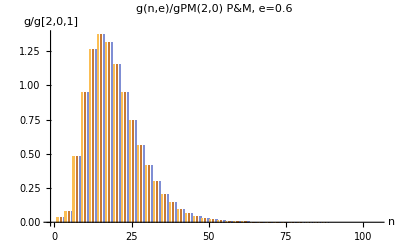

```mathematica
Module[{nmax=7, ecc=0.6},
Show[
BarChart[ Table[
{gg[n,ecc]/ggPM[2,0],ggPM[n,ecc]/ggPM[2,0], ggAS[n,ecc]/ggPM[2,0]},{n, 1,40}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/gPM(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
]
```

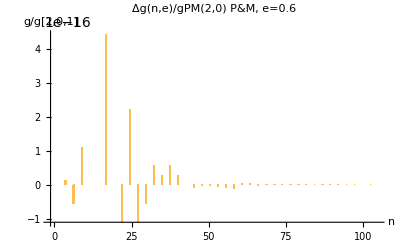

```mathematica
Module[{nmax=7, ecc=0.6},
Show[
BarChart[ Table[
{(gg[n,ecc]-ggPM[n,ecc])/ggPM[2,0],(ggPM[n,ecc]-ggPM[n,ecc])/ggPM[2,0], (ggAS[n,ecc]-ggPM[n,ecc])/ggPM[2,0]},{n, 1,40}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["Δg(n,e)/gPM(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
]
```